```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-((2857-(5033/9)Nf+(325/27) Nf^2)/128); (*for Nc=3 only*)
β3[Nf_]=((-1)/256)((149753/6+3564 Zeta[3])-(1078361/162+(6508/27) Zeta[3])Nf+(50065/162+(6472/81)Zeta[3])Nf^2+(1093/729) Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=(1/16)(202/3-(20/9)Nf);(*for Nc=3 only*)
γ2[Nf_]=(1/64)(1249+(-(2216/27)-(160/3) Zeta[3])Nf-(140/81) Nf^2);(*for Nc=3 only*)
γ3[Nf_]=(1/256)(4603055/162+(135680/27) Zeta[3]-8800Zeta[5]+(-(91723/27)-(34192/9) Zeta[3]+880 Zeta[4]+(18400/9)Zeta[5])Nf+(5242/243+(800/9) Zeta[3]-(160/3)Zeta[4])Nf^2+(-(332/243)+(64/27) Zeta[3])Nf^3);

b0[Nf_]=-((8β0[Nf])/(2(4π)^2));
b1[Nf_]=-((32 β1[Nf])/(2(4π)^2));

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=(-1)/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-( β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+(1/(β0[Nf]^7 t^4))( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Function Definitions

```mathematica
kfinal={0.6802525363662164,-0.31465604392609736};(*100k run*)
kfinalu={0.9017845365143496,-0.3669424499609976};
kfinall={0.4587205362180833,-0.26236963789119705};
αcont={0.5146004500017507,0.002579680095957094};(*10k run*)
σcont={0.16904257426266697,0.0009046347484072015};
ccont={-0.15782092474161866,0.0024785523617348124};
rsbvac=1.542442506842263/conv;
Tset={0.15,0.16,0.17,0.18,0.19,0.2,0.25,0.3};
TsetS={"T=150MeV","T=160MeV","T=170MeV","T=180MeV","T=190MeV","T=200MeV","T=250MeV","T=300MeV","Vacuum"};
```

```mathematica
mDcalmu[T_,μ_,c_,d_]:=Re[Sqrt[Nc/3+nF/6+nF/(2 π^2)(μ/3)^2/T^2]g4[2π √(T^2+μ^2/π^2)]T+1/(4π)Nc g4[2π √(T^2+μ^2/π^2)]^2 T Log[Sqrt[Nc/3+nF/6]/g4[2π √(T^2+μ^2/π^2)]]+c g4[2π √(T^2+μ^2/π^2)]^2 T+d g4[2π √(T^2+μ^2/π^2)]^3 T ];
```

```mathematica
ReVs[r_,mD_,σ_]:=(2 σ)/mD-(ⅇ^(-mD r) (2+mD r) σ)/mD;
ReVc[r_,mD_,α_,c_]:=c-α mD-α Exp[-mD r]/r;
ReV[r_,mD_,α_,σ_,c_]:=c-α mD-α Exp[-mD r]/r+(2 σ)/mD-(ⅇ^(-mD r) (2+mD r) σ)/mD;
ReVm0[r_,α_,σ_,c_]:=c-α/r+σ r;
```

```mathematica
ImVc[r_,mD_,α_,T_]:=T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4]);
ImVs[r_,mD_,σ_,T_]:=1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
ImV[r_,mD_,α_,σ_,T_]:=(T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4])+1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4]);
```

## Plots for physical values

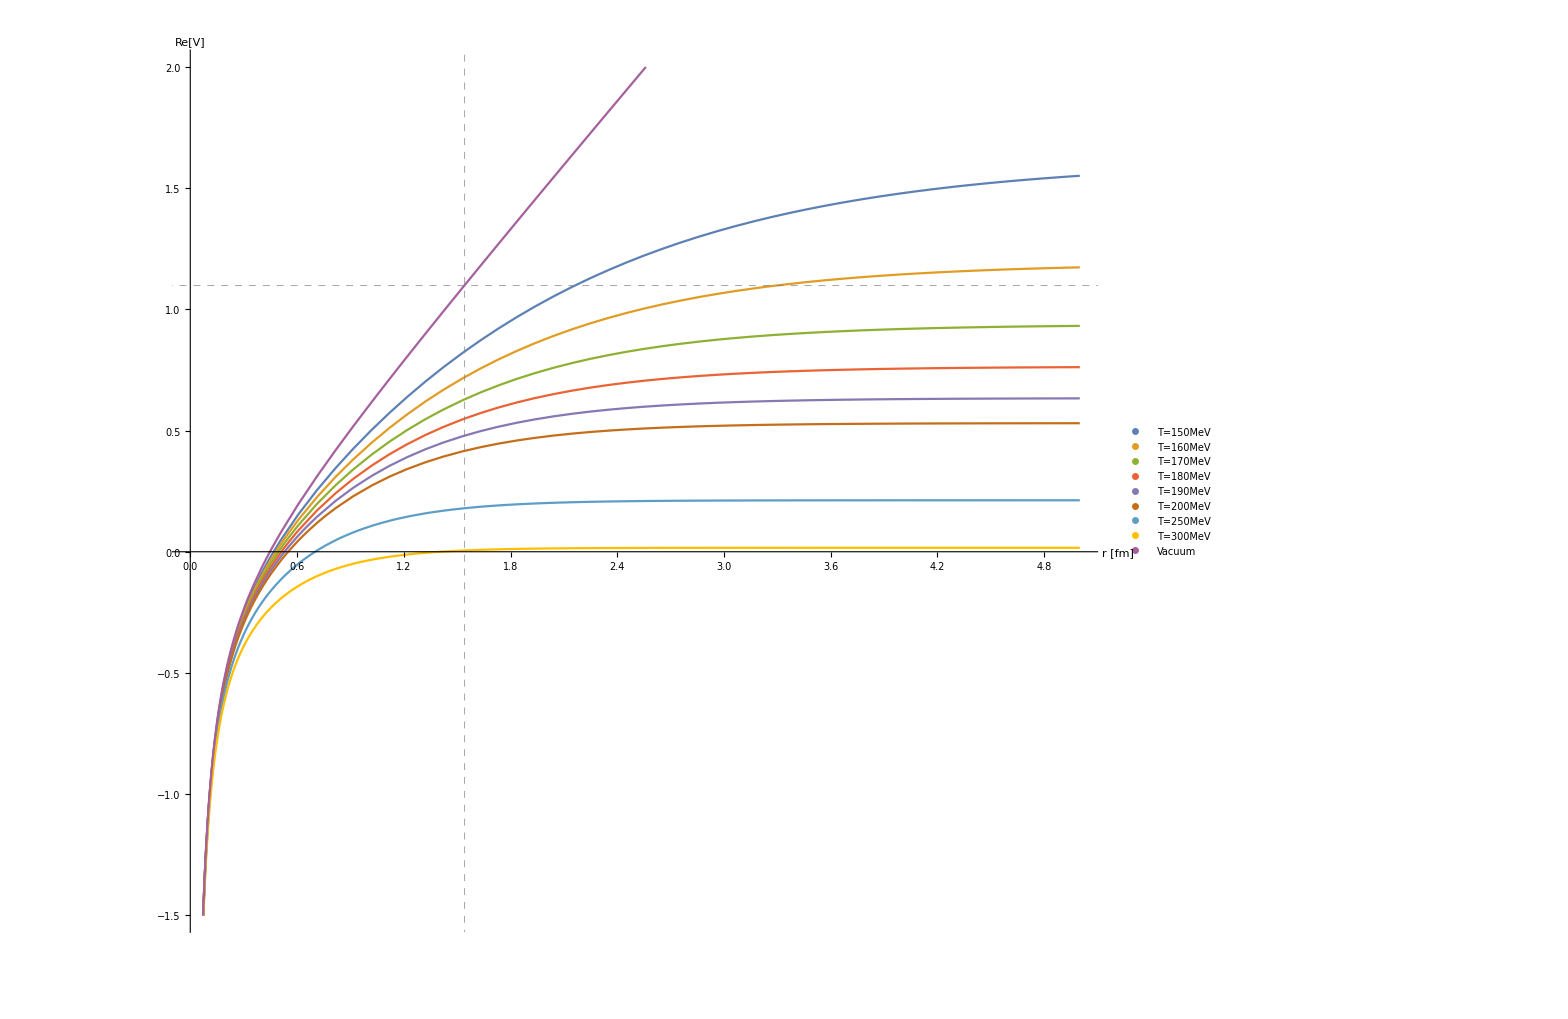

```mathematica
Plot[{ReV[r/0.197,mDcalmu[Tset[[1]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[2]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[3]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[4]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[5]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[6]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[7]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[8]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReVm0[r/0.197,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{1200,1200},PlotRange->{-1.5,2},GridLines->{{rsbvac conv},{ReVm0[rsbvac,αcont[[1]],σcont[[1]],ccont[[1]]]}},GridLinesStyle->Directive[Gray, Dashed],PlotLegends->Placed[PointLegend[TsetS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.8,0.95}],BaseStyle->{FontSize->14}]
```

```mathematica
ReVas[t_]:=ccont[[1]]-αcont[[1]]mDcalmu[t,0,kfinal[[1]],kfinal[[2]]]+(2 σcont[[1]])/mDcalmu[t,0,kfinal[[1]],kfinal[[2]]];
```

```mathematica
rsbth=Table[{t,r/.FindRoot[ReV[r/0.197,mDcalmu[t/1000,0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==0.99ReVas[t/1000],{r,1/10,1/100,10}]},{t,170,300,10}]
```

{{170,4.54402},{180,4.03138},{190,3.66671},{200,3.39367},{210,3.18835},{220,3.02626},{230,2.89575},{240,2.79176},{250,2.71159},{260,2.65484},{270,2.62413},{280,2.62795},{290,2.69204},{300,2.94295}}

```mathematica
mdinv=Table[{t,conv/mDcalmu[t/1000,0,kfinal[[1]],kfinal[[2]]]},{t,150,300,10}]
```

{{150,1.08798},{160,0.855893},{170,0.721273},{180,0.63156},{190,0.566487},{200,0.516531},{210,0.477741},{220,0.445811},{230,0.418587},{240,0.395021},{250,0.374366},{260,0.356073},{270,0.339729},{280,0.325014},{290,0.311679},{300,0.299525}}

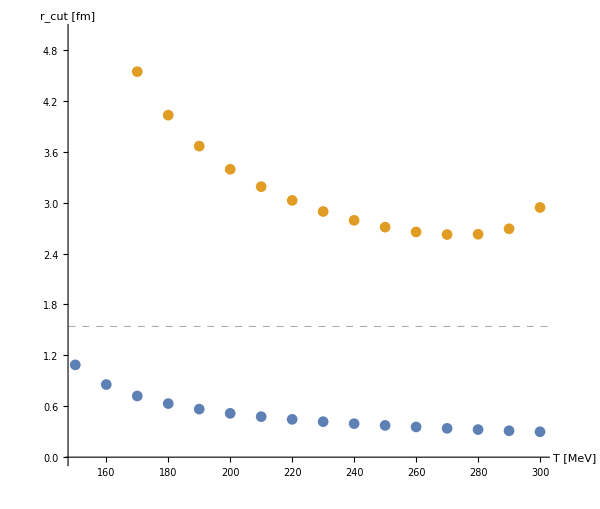

```mathematica
ListPlot[{mdinv,rsbth},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [MeV]","r_cut [fm]"},ImageSize->{600,600},BaseStyle->{FontSize->14},GridLines->{{},{rsbvac conv}},GridLinesStyle->Directive[Gray, Dashed],PlotRange->{0.,5}]
```

```mathematica
mdTset=Table[{t,mDcalmu[t/1000,0,kfinal[[1]],kfinal[[2]]]},{t,150,300,10}]
```

{{150,0.18137},{160,0.230551},{170,0.273582},{180,0.312444},{190,0.348334},{200,0.382023},{210,0.413042},{220,0.442625},{230,0.471412},{240,0.499536},{250,0.527096},{260,0.554175},{270,0.580837},{280,0.607134},{290,0.63311},{300,0.6588}}

```mathematica
rsbinvth=Table[{t,conv r/.FindRoot[ReV[r/0.197,mDcalmu[t/1000,0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==0.99ReVas[t/1000],{r,1/10,1/100,10}]},{t,170,300,10}]
```

{{170,0.896658},{180,0.7955},{190,0.723541},{200,0.669663},{210,0.629147},{220,0.597163},{230,0.57141},{240,0.550889},{250,0.53507},{260,0.523872},{270,0.517811},{280,0.518565},{290,0.531211},{300,0.580723}}

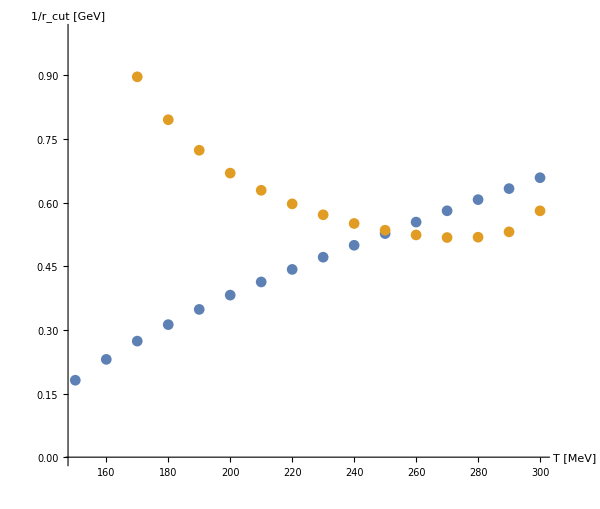

```mathematica
ListPlot[{mdTset,rsbinvth},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [MeV]","1/r_cut [GeV]"},ImageSize->{600,600},BaseStyle->{FontSize->14},PlotRange->{0.,1}]
```

## Plots for lattice fits

```mathematica
Tlat={0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861};
αlat={0.4859592638209618,0.47104500698378393,0.4561307501466063,0.4374879291001341,0.41884510805366193,0.411387979635073,0.384542317328153};
σlat={0.2088434405704896,0.21706585496978287,0.22528826936907603,0.23556628736819257,0.245844305367309,0.24995551256695564,0.26475585848568345};
clat={1.6313652574133624,1.7808011444057126,1.9302370313980628,2.117031890138499,2.303826748878935,2.37854469237511,2.6475292889613407};
```

```mathematica
mdlat={0.06997549222118046,0.18764366844838265,0.25469933582761983,0.3734921779850663,0.5267111789784007,0.5405169214400376,0.6676534051261366};
```

```mathematica
TlatS={"T=41MeV","T=72MeV","T=148MeV","T=164MeV","T=182MeV","T=205MeV","T=232MeV","T=243MeV","T=286MeV"};
```

```mathematica
conv=0.197327;
```

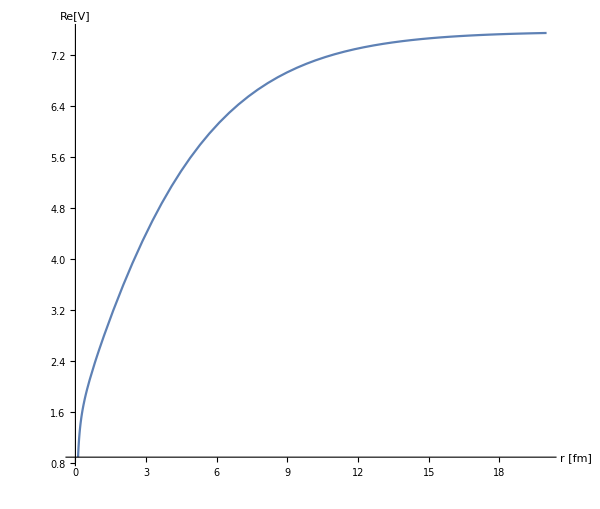

```mathematica
Block[{l=1},Plot[ReV[r/conv,mdlat[[l]],αlat[[l]],σlat[[l]],clat[[l]]],{r,0,20},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600}]]
```

```mathematica
ReVlatplot=Table[ReV[r/conv,mdlat[[l]],αlat[[l]],σlat[[l]],clat[[l]]]-clat[[l]]-0.45l+5.,{l,1,7}];
```

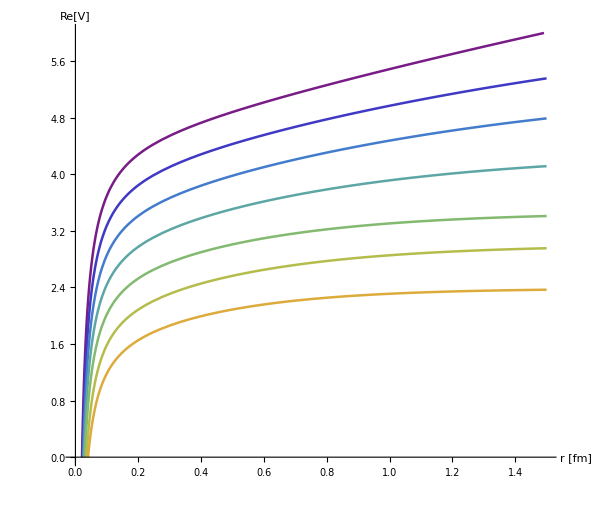

```mathematica
ReVlatanPlot=Plot[ReVlatplot,{r,0.001,1.5},PlotRange->{{0.00001,1.5},{0.,6}},PlotStyle->Thread@{AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[0,1,1/8]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600},PlotRange->{{0,1.5},All},PlotLegends->Placed[PointLegend[TlatS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.8,0.1}],BaseStyle->{FontSize->14}]
```

```mathematica
ReVlatas[n_]:=clat[[n]]-αlat[[n]]mdlat[[n]]+(2 σlat[[n]])/mdlat[[n]];
```

```mathematica
rsbthlat=Table[{Tlat[[n]],r/.FindRoot[ReV[r/conv,mdlat[[n]],αlat[[n]],σlat[[n]],clat[[n]]]==0.99ReVlatas[n],{r,1/10,1/100,30}]},{n,1,7}]
```

{{0.1478,16.1267},{0.1642,5.63785},{0.1818,4.01413},{0.2054,2.59841},{0.2317,1.74156},{0.2425,1.68421},{0.2861,1.30083}}

```mathematica
mdlatinv=Table[{Tlat[[n]],conv/mdlat[[n]]},{n,1,7}]
```

{{0.1478,2.81994},{0.1642,1.0516},{0.1818,0.774745},{0.2054,0.52833},{0.2317,0.37464},{0.2425,0.365071},{0.2861,0.295553}}

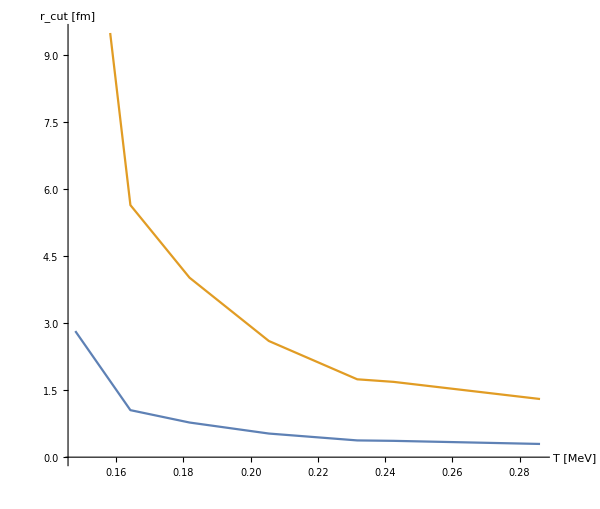

```mathematica
ListPlot[{mdlatinv,rsbthlat},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [MeV]","r_cut [fm]"},ImageSize->{600,600},BaseStyle->{FontSize->14},Joined->True]
```

```mathematica
mdlatset=mdlatinv=Table[{Tlat[[n]],mdlat[[n]]},{n,1,7}]
```

{{0.1478,0.0699755},{0.1642,0.187644},{0.1818,0.254699},{0.2054,0.373492},{0.2317,0.526711},{0.2425,0.540517},{0.2861,0.667653}}

```mathematica
rsbinvth=Table[{Tlat[[n]],conv r/.FindRoot[ReV[r/0.197,mdlat[[n]],αlat[[n]],σlat[[n]],clat[[n]]]==0.99ReVlatas[n],{r,1/10,1/100,20}]},{n,1,7}]
```

{{0.1478,3.17697},{0.1642,1.11066},{0.1818,0.790784},{0.2054,0.511886},{0.2317,0.343088},{0.2425,0.33179},{0.2861,0.256263}}

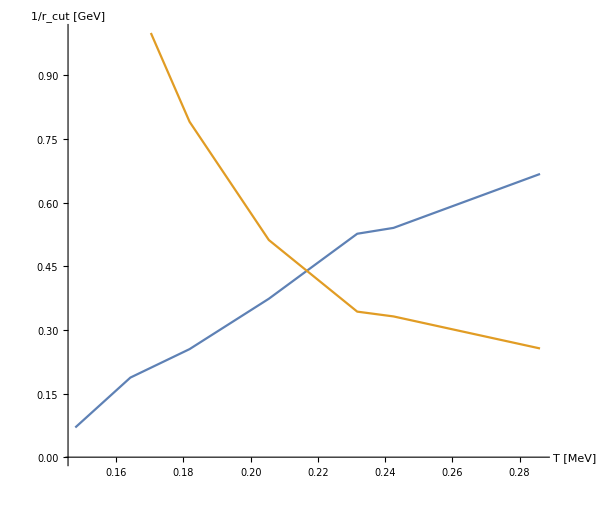

```mathematica
ListPlot[{mdlatset,rsbinvth},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [MeV]","1/r_cut [GeV]"},ImageSize->{600,600},BaseStyle->{FontSize->14},PlotRange->{0.,1},Joined->True]
```

### Check ImV for lattice fits with different regulators

```mathematica
rImϵr[r_,mD_,T_,reg_]:=2r mD T Quiet[NIntegrate[p^2(p mD^2)/((p^2+reg^2)^(1/2)(p^2+mD^2)^2)Sin[p r],{p,0,∞},MaxRecursion->20]];
```

```mathematica
ImVsregTab[mD1_,σ1_,T1_,reg1_,n_]:=Block[{mD=mD1,σ=σ1,T=T1,reg=reg1,tab0,tab1,inter0,inter1,inter2,tab2,rϵinter},
rϵinter=Quiet[Interpolation[ParallelTable[{r,rImϵr[r,mD,T,reg]},{r,0,150,1/100}]]];
inter0[r_]:=Quiet[NIntegrate[rϵinter[r1],{r1,0,r},MaxRecursion->20]];
tab1=ParallelTable[{r,inter0[r]},{r,0,150,1/100}];
inter1=Interpolation[tab1];
inter2[r_]:=NIntegrate[inter1[r1],{r1,0,r}];
tab2=ParallelTable[{r,inter2[r]},{r,0,150,1/100}];
Export["mathematica/vel_pot/ImVsrregT"<>ToString[n]<>".dat",tab2];
Return[Interpolation[tab2]]];
```

```mathematica
ImVsT1interMD=ImVsregTab[mdlat[[1]],σlat[[1]],Tlat[[1]],mdlat[[1]],1];
ImVsT2interMD=ImVsregTab[mdlat[[2]],σlat[[2]],Tlat[[2]],mdlat[[2]],2];
ImVsT3interMD=ImVsregTab[mdlat[[3]],σlat[[3]],Tlat[[3]],mdlat[[3]],3];
ImVsT4interMD=ImVsregTab[mdlat[[4]],σlat[[4]],Tlat[[4]],mdlat[[4]],4];
ImVsT5interMD=ImVsregTab[mdlat[[5]],σlat[[5]],Tlat[[5]],mdlat[[5]],5];
ImVsT6interMD=ImVsregTab[mdlat[[6]],σlat[[6]],Tlat[[6]],mdlat[[6]],6];
ImVsT7interMD=ImVsregTab[mdlat[[7]],σlat[[7]],Tlat[[7]],mdlat[[7]],7];
```

```mathematica
ImVsT1intersb=ImVsregTab[mdlat[[1]],σlat[[1]],Tlat[[1]],rsbinvth[[1,2]],1];
ImVsT2intersb=ImVsregTab[mdlat[[2]],σlat[[2]],Tlat[[2]],rsbinvth[[2,2]],2];
ImVsT3intersb=ImVsregTab[mdlat[[3]],σlat[[3]],Tlat[[3]],rsbinvth[[3,2]],3];
ImVsT4intersb=ImVsregTab[mdlat[[4]],σlat[[4]],Tlat[[4]],rsbinvth[[4,2]],4];
ImVsT5intersb=ImVsregTab[mdlat[[5]],σlat[[5]],Tlat[[5]],rsbinvth[[5,2]],5];
ImVsT6intersb=ImVsregTab[mdlat[[6]],σlat[[6]],Tlat[[6]],rsbinvth[[6,2]],6];
ImVsT7intersb=ImVsregTab[mdlat[[7]],σlat[[7]],Tlat[[7]],rsbinvth[[7,2]],7];
```